## Misc Utilities

```mathematica
quickHist[dataAsList_,plotLbls_, sz_:Medium]:=
Labeled[
Histogram[dataAsList,Automatic,"Probability",
ImageSize->sz,
ChartStyle->Table[ColorData[3,2*n],{n,1, Length@dataAsList}],
ChartLegends->Table[Style[lbl,FontFamily->"Courier"],{lbl,plotLbls}]
],
{Rotate["",90 Degree],""},{Left,Bottom}
]
```

### Activation Functions

```mathematica
swish=ElementwiseLayer[#*LogisticSigmoid[#]&];
gauss[s_] := Exp[-s^2/2]/Sqrt[2 Pi];
ψ[s_] := Erfc[s/Sqrt[2]]/2;
ψInv[u_] := Sqrt[2]* InverseErfc[2*u];
φ[s_] := s*ψ[-s] + gauss[-s];
transducerφ[s_] :=φ[s]-φ[0];
grelu=ElementwiseLayer[transducerφ[#]&];
```

### Functions on Sequences

```mathematica
ClearAll[generateF3,normalizedF3,jacobiF3]

generateF3[η_]:=2*η*Sinh[η]*Divide[Exp[-η*Sinh[η]]-Exp[-η],1-Sinh[η]]
normalizedF3[η_]:=generateF3[η]/generateF3[Sqrt[2]]
jacobiF3[η_]:=normalizedF3[η+Sqrt[2.]]
```

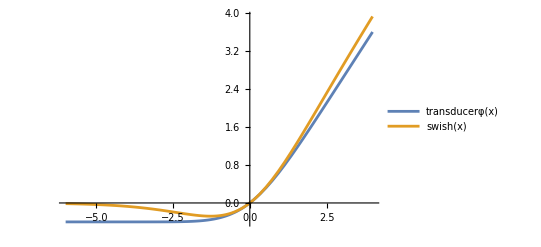
-Graphics- | -Graphics-

```mathematica
Multicolumn[{Plot[{generateF3[η], jacobiF3[η],LogisticSigmoid[η]},{η, -0.5,0.5}, PlotLabels->"Expressions", ImageSize->300],
Plot[{transducerφ[x],swish[x]},{x,-6,4}, PlotLegends->"Expressions"]},2]
```

### Data: all of Shakespeare’s plays tokenized and presented as lines of text

```mathematica
(*lines=linesOfShakespeare=Import["/Users/kinjeketileii/Library/Mobile Documents/com~apple~CloudDocs/2024/Ouroboros/ProcessedShakespeareLines.wl"];*)

lines=linesOfShakespeare=Import["/Users/kinjeketile/Library/Mobile Documents/com~apple~CloudDocs/2024/Ouroboros/ProcessedShakespeareLines.wl"];
vocabulary=Union[Flatten[lines]];
lexicon=vocabulary;
StringForm["Shakespeare wrote a staggering `` lines",Length@lines]
StringForm["nanoGPT experiences these lines in the form: ``!",RandomSample[lines,1]]

StringForm["Shakespeare's plays constitute a vocabulary of size ``",Length@vocabulary]
"random sample of vocabulary"->RandomSample[vocabulary,9]
```

Shakespeare wrote a staggering 108755 lines

nanoGPT experiences these lines in the form: {{Now,, ,by, ,the, ,jealous, ,queen, ,of, ,heaven,, ,that, ,kiss,$End}}!

Shakespeare's plays constitute a vocabulary of size 27713

random sample of vocabulary→{murkiest,basin,pyramides,gravely,Jovial,vaunter,misapplied,extinct,languish}

### Embed Token Sequences

```mathematica
encodeLexicon[embdims_, lexicon_] :=
		FunctionLayer[
			Module[{emb1, emb2, posembed},
				emb1 = EmbeddingLayer[embdims][#Input];
				posembed = SequenceIndicesLayer[2^6][#Input];
				emb2 = EmbeddingLayer[embdims][posembed];
				emb1 + emb2
			]&
			,
			"Input" -> {"Varying", NetEncoder[{"Class", lexicon}]}
		]//NetInitialize
		
encodeLexicon[2, vocabulary]
```

FunctionLayer[<>]

## Atoms

## EntryPoint

### Basic Constructors

```mathematica
ClearAll[delaySequence,oPlus,oDot, scaling8r, mlp, linearNetMap]

delaySequence =PaddingLayer[{{1, 0}, {0, 0}}];
advanceSequence=PaddingLayer[{{0,1},{0,0}}];

mlp[dout_]:=LinearLayer[dout,"Biases"->None]

linearNetMap[dout_]:=NetMapOperator[mlp[dout]]

oPlus:=FunctionLayer[
Module[{},
Identity[#Input1] +Identity[#Input2] 
]&
]//NetInitialize

oDot:=FunctionLayer[
Module[{},
Identity[#Input1]*Identity[#Input2] 
]&
]//NetInitialize

scaling8r[dims_,scale_:Automatic]:=FunctionLayer[
Module[{},
NormalizationLayer[2,"Same","Input"->{"Varying",dims},"Scaling"->scale][#Input]
]&
]//NetInitialize

multBy[scale_:1.]:=FunctionLayer[
Module[{},
scale*Identity[#Input]
]&
]

display=False;
If[display, 
Multicolumn[{"delay"->delaySequence,"oPlus"->oPlus,"oDot"->oDot, "scaling8r"->scaling8r[4]},2]
]
```

### Elaborate constructors

tokenseq={{Cordelia,, ,Cordelia,! ,stay, ,a, ,little,. ,Ha,!,$End}}

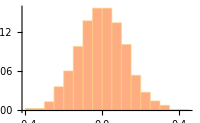
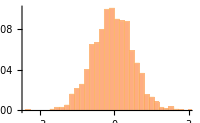
-Graphics-
-Graphics-
-Graphics-

```mathematica
ClearAll[moserSequence,seqvelocity,seqVelocity,stepωQKseqζ]

seqVelocity:=FunctionLayer[
Module[{delayseq,advanceseq},
delayseq=delaySequence[Most[#Input]];
advanceseq=advanceSequence[Rest[#Input-delayseq]]
]&
,"Input" -> Automatic
]//NetInitialize

pseudoCosQK[nstates_, dcell_] :=FunctionLayer[
Module[{vel, xWQ,xWK,ωQK},
vel=seqVelocity[#Input];
xWQ=linearNetMap[nstates][vel];
xWK=linearNetMap[nstates][vel];
ωQK=scaling8r[nstates][linearNetMap[dcell][xWQ*xWQ]]
]&
,"Input" -> {"Varying",dcell}
]//NetInitialize




moserSequence[dims_] :=NetInitialize@FunctionLayer[
Module[{pseudocos},
(*pseudocos=(1-Tanh[linearNetMap[dims][#Input]])/2;
scaling8r[dims][jacobiF3[-pseudocos]]*)
scaling8r[dims][#Input]
]& ,"Input" -> {"Varying",dims}
]

steplnZ[dcell_] :=NetInitialize@FunctionLayer[
Module[{},
#State+Log[1+Exp[#Input-#State]]
]& ,"Input" -> {dcell}, "State" -> {dcell}
]

pressureKac[dcell_]:=NetFoldOperator[steplnZ[dcell]]

stepHJKB[dcell_] :=FunctionLayer[
Module[{Γ},
Γ=Divide[1, 1+Exp[#δν-#lnZ]];
Γ*#State+(1-Γ)*#Input
]&
,"Input" -> {dcell},"State" -> {dcell},"δν"->{dcell}, "lnZ"->{dcell}
]//NetInitialize

gener8HJKBseq[dcell_]:=NetFoldOperator[stepHJKB[dcell]]



propg8rHJKB[nstates_, dcell_] :=FunctionLayer[
Module[{xWQ,xWK,WQxWKx,ωQK, softmaxωQK},
xWQ=linearNetMap[nstates][#Input];
xWK=linearNetMap[nstates][#Input];
WQxWKx=scaling8r[nstates][xWQ*xWQ];
ωQK= linearNetMap[dcell][WQxWKx];
softmaxωQK=SoftmaxLayer[1][-ωQK]
]&
,"Input" -> {"Varying",dcell}
]//NetInitialize




stepωQKseqζ[dcell_] :=FunctionLayer[
Module[{propg8seq,seqlen, seqζ},
seqlen=Log[Length[#Input]];
seqζ=mlp[dcell][#Input];
propg8seq=#softmaxωQK*#State+(1-#softmaxωQK)*seqζ;
seqlen*propg8seq
]&
,"Input" -> {dcell},"State" -> {dcell},"softmaxωQK"->{dcell}
]//NetInitialize



dims=embdims=celldims=2^7; nstates=2^4;
tokseq=RandomSample[lines, 1];
StringForm["tokenseq=``", tokseq]
embseq=encodeLexicon[embdims, vocabulary][tokseq];

seqlen=Length@embseq;
cosseq=KroneckerProduct[Range[1,seqlen],ConstantArray[1,embdims]];
cosseq=Cos[2*N[Pi]*(cosseq/seqlen)];

Table[
opHJKB=NetFoldOperator[stepωQKseqζ[dims]];
propg8r = propg8rHJKB[nstates,dims][seq] ;
pathIntegral=scaling8r[dims,1.]@opHJKB[<|"Input" ->seq,"softmaxωQK" ->propg8r|>];
pathIntegralII=moserSequence[dims][opHJKB[<|"Input" ->seq,"softmaxωQK" ->propg8r |>]
];

Multicolumn[
{quickHist[{Flatten@N@seq},{"embed[tokenseq]"}, 200],
quickHist[{Flatten@pathIntegral},{"layerNorm@∫HJKB[embed]"},200],
quickHist[{Flatten@pathIntegralII},{"F3Norm@∫HJKB[embed]"},200]
}
,1],{seq,{embseq}}]//First
```

### HJKB Cell

```mathematica
embseq=encodeLexicon[embdims, vocabulary][RandomSample[lines, 1]];
incoming=embseq;
ref = moserSequence[dcell][incoming]; (* input ->{Nseq, embdims}, output -> {Nseq, dcell} *)
softmaxωQK=propg8rHJKB[nstates,dcell][ref ]; (* nstates is internal to propg8rHJKB 
and softmaxωQK always has shape {Nseq, dcell}*)
HJKBƒdt=NetFoldOperator[stepωQKseqζ[dcell]][<|"Input" ->ref,"softmaxωQK" ->softmaxωQK |>];
moserSequence[dcell][ref+HJKBƒdt];
```

```mathematica
ClearAll[HJKBCell, interposer, interposerNorm]
HJKBCell[nstates_,dcell_]:=NetGraph[{
"ref"->linearNetMap[dcell],
"ζ"-> scaling8r[dcell][linearNetMap[dcell]],
"δν"->pseudoCosQK[nstates,dcell],
"lnZ" -> pressureKac[dcell],
"∫HJKB"->gener8HJKBseq[dcell],
"∑"->oPlus,
"remastered"->scaling8r[dcell]
},
{
NetPort["Input"]->"ζ",
NetPort["Input"]->"ωQK",
NetPort["Input"]->"lnZ",
"δν"->"∫HJKB","lnZ"->"∫HJKB","ζ"->"∫HJKB",
"∫HJKB"->"∑",
"ref"->"∑","∑"->"remastered",
"remastered"->NetPort["Output"]
},
"Input"->{"Varying",Automatic}
]//NetInitialize
```

```mathematica
ClearAll[HJKBCell, interposer, interposerNorm]
HJKBCell[nstates_,dims_]:=NetGraph[{
"ref"->moserSequence[dims],
"softmaxωQK"->propg8rHJKB[nstates,dims],
"∫dt"->NetFoldOperator[stepωQKseqζ[dims]],
"∑"->oPlus,
"remastered"->moserSequence[dims]
},
{
NetPort["Input"]->"ref",
"ref"->"softmaxωQK",
"ref"->"∫dt","softmaxωQK"->"∫dt","∫dt"->"∑",
"ref"->"∑","∑"->"remastered",
"remastered"->NetPort["Output"]
},
"Input"->{"Varying",Automatic}
]//NetInitialize

interposerNorm[dims_] :=NetInitialize@FunctionLayer[Module[{},
(*scaling8r[dims][jacobiF3[-(1-Tanh[#Input])/2]]*)
scaling8r[dims][#Input]
]& ,"Input" -> {"Varying",dims}
]

interposer[dims_] := NetInitialize@NetGraph@FunctionLayer[
Module[{seq},
seq = LinearLayer[4 dims] /@ #Input;
seq = ElementwiseLayer["GELU"][seq];seq = LinearLayer[dims] /@ seq;interposerNorm[dims][seq + #Input]
]
&,"Input" -> {"Varying", dims}]

HJKBCell[2^4,2^7]
interposerNorm[2^7]
```

NetGraph[…]

FunctionLayer[…]

```mathematica
(*results=Association[];
embdims=2^7; celldims=2^8; nstates=2^4;
tokseq={"To"," ","be",","," ","or"," ","not"," ","to","be"};

StringForm["embseq=emb[``]", tokseq]
embseq=encodeLexicon[embdims, vocabulary][tokseq];

seqlen=Length@embseq;
unitCell=OuroborosCell[nstates,celldims,embdims];
results["data"]=unitCell[embseq];
cosseq=KroneckerProduct[Range[1,seqlen],ConstantArray[1,embdims]];
cosseq=Cos[2*N[Pi]*(cosseq/seqlen)];
results["cos"]=unitCell[cosseq];


Multicolumn[{"embseq"->ArrayPlot[embseq,AspectRatio->0.75],
"unitCell[embseq]"->ArrayPlot[results["data"],AspectRatio->0.75],
"cosseq"->ArrayPlot[cosseq,AspectRatio->0.75],
"unitCell[cosseq]"->ArrayPlot[results["cos"],AspectRatio->0.75]},2]


Multicolumn[
Table[{
ListPlot[{embseq[[All,m]], results["data"][[All,m]]}, Filling->Bottom,PlotLabels->{"embseq","cell[embseq]"}, ImageSize->300],
quickHist[{embseq[[All,m]],results["data"][[All,m]]},{"in", "out"}, 250]},
{m, RandomSample[Range@nstates,1]}]//Flatten
,2]

Multicolumn[
Table[{
ListPlot[{cosseq[[All,m]], results["cos"][[All,m]]}, Filling->Bottom,PlotLabels->{"in","out"}, ImageSize->300],
quickHist[{cosseq[[All,m]],results["cos"][[All,m]]},{"cosseq", "cell[cosseq]"}, 250]},
{m, RandomSample[Range@nstates,1]}]//Flatten
,2]*)
```

## Decoder

```mathematica
ClearAll[decoder]
decoder[demb_, dcell_, nstates_, nblocks_,vocabulary_] := Module[
{embed, retouch},
embed = encodeLexicon[demb, vocabulary];
retouch =NetFlatten@NetChain[{ HJKBCell[nstates,dcell], interposer[dcell]}];
	NetInitialize@NetGraph@FunctionLayer[
		Module[
			{original, remastered},
			original=embed[#Input];
			remastered=retouch[original];
			Table[remastered=retouch[remastered], nblocks-1];
			SoftmaxLayer[]/@LinearLayer[]/@remastered
		]&,
		"Input" -> {"Varying", NetEncoder[{"Class", vocabulary}]},
		"Output"-> {"Varying", NetDecoder[{"Class", vocabulary}]}
	]
]
decoder[128,128,4,3,vocabulary]
```

NetGraph[<5>, <6>]

## End-to-End

```mathematica
ClearAll[end2end, initialState]
embdims=2^7; celldims=2^7; nstates=2^4;ncells=4;
end2end=decoder[embdims,celldims,nstates,ncells, vocabulary]
initialState=NetGraph@FunctionLayer[
Module[{encode,decode,most,rest},
most=Most[#Input];
rest=Rest[#Input];
decode=end2end[most];
CrossEntropyLossLayer["Index"][{decode,rest}]]&,
"Input" -> {"Varying", NetEncoder[{"Class", vocabulary}]}
]
```

NetGraph[<6>, <7>]

NetGraph[<4>, <6>]

### Train

```mathematica
ClearAll[trainee]
trainee=NetTrain[initialState,linesOfShakespeare,All,MaxTrainingRounds->1,ValidationSet->Scaled[0.1],BatchSize->16, LearningRate->0.001]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24  rounds:0  time:15s  examples/s:27.
data | ,,  training examples:97888  validation examples:10880  processed examples:384  skipped examples:0
method | ,,  ADAMoptimizer  batch size16CPU
round | ,,  loss: —   error: — 
validation | ,,  loss: —   error: — 
 | 
-Graphics-  training set	-Graphics-  validation set | ]

#### Serialize/Load

```mathematica
trainedState=NetExtract[trainee["TrainedNet"], "decode"];
savePath="/Users/kinjeketileii/Library/Mobile Documents/com~apple~CloudDocs/2024//models/checkpoints/trainedState.wxf";
Export[savePath, trainedState];
```

Export::nodir: Directory /Users/kinjeketileii/Library/Mobile Documents/com~apple~CloudDocs/2024/models/checkpoints/ does not exist.

Export::noopen: Cannot open /Users/kinjeketileii/Library/Mobile Documents/com~apple~CloudDocs/2024//models/checkpoints/trainedState.wxf.

### Initial 𝔾

### Create end-to-end decoder

### Resume ...

```mathematica
(*trainedState = Import[savePath];*)
```

```mathematica
predictor=NetReplacePart[trainedState,{{"output",1}->{SequenceLastLayer[],NetExtract[trainedState,{"output",1,"Net"}]},{"output",2}->NetExtract[trainedState,{"output",2,"Net"}],"Input"->{"Varying",NetEncoder[{"Class",vocabulary}]},"Output"->NetDecoder[{"Class",vocabulary}]}]
```

NetGraph[<6>, <7>]

```mathematica
Column@NestWhileList[Append[#,predictor[#]]&,{"O"},Last[#]!="$End"&,1,15]
```

```mathematica
Manipulate[Column@NestWhileList[Append[#,predictor[#,"RandomSample"->{"Temperature"->β}]]&,{"O"},Last[#]!="$End"&,1,37],{β,1/Sqrt[2.], Sqrt[2.]}]
```

```mathematica
Column@NestWhileList[Append[#,predictor[#,"RandomSample"->{"Temperature"->1.33}]]&,{"O"},Last[#]!="$End"&,1,37]
```

```mathematica
Column@NestWhileList[Append[#,predictor[#,"RandomSample"->{"TopProbabilities"->3}]]&,{"O"},Last[#]!="$End"&,1,25]
```

```mathematica
upperCaseWords=Select[vocabulary,UpperCaseQ[StringTake[#,1]]&& LowerCaseQ[StringDrop[#,1]]&];

Length@upperCaseWords
RandomSample[upperCaseWords,5]
Column@Table[StringJoin@Most@NestWhile[Append[#,predictor[#,"RandomSample"->{"Temperature"->.78}]]&,RandomSample[upperCaseWords,1],Last[#]!="$End"&,33,1],12]
```

6735

{Ancient,Faith,Wide,Auvergne,Cliffords}

Corin
Smithfield
Tiber
Chiefly
Bottom
Admits
Infer
Refusing
Vexing
Convey
Antipodes
Avoid

```mathematica
RandomSample[lines,7]
```

```mathematica
traineeOuroboros=Import["/Users/kinjeketileii/Library/Mobile Documents/com~apple~CloudDocs/2024/models/checkpoints/traineeOuroboros.wxf"];
traineeAttn=Import["/Users/kinjeketileii/Library/Mobile Documents/com~apple~CloudDocs/2024/models/checkpoints/traineeTransformer.wxf"];
```

```mathematica
(*trainedState=NetExtract[traineeOuroboros["TrainedNet"], "decode"];
predictor=NetReplacePart[trainedState,{{"output",1}->{SequenceLastLayer[],NetExtract[trainedState,{"output",1,"Net"}]},{"output",2}->NetExtract[trainedState,{"output",2,"Net"}],"Input"->{"Varying",NetEncoder[{"Class",vocabulary}]},"Output"->NetDecoder[{"Class",vocabulary}]}]

upperCaseWords=Select[vocabulary,UpperCaseQ[StringTake[#,1]]&& LowerCaseQ[StringDrop[#,1]]&];*)


Column@Table[StringJoin@Most@NestWhile[Append[#,predictor[#,"RandomSample"->{"Temperature"->.81}]]&,RandomSample[vocabulary,1],Last[#]!="$End"&,1,23],10]
```

```mathematica
trainedState=NetExtract[traineeAttn["TrainedNet"], "decode"];
predictor=NetReplacePart[trainedState,{{"output",1}->{SequenceLastLayer[],NetExtract[trainedState,{"output",1,"Net"}]},{"output",2}->NetExtract[trainedState,{"output",2,"Net"}],"Input"->{"Varying",NetEncoder[{"Class",vocabulary}]},"Output"->NetDecoder[{"Class",vocabulary}]}]

upperCaseWords=Select[vocabulary,UpperCaseQ[StringTake[#,1]]&& LowerCaseQ[StringDrop[#,1]]&];
Column@Table[StringJoin@Most@NestWhile[Append[#,predictor[#,"RandomSample"->{"Temperature"->Sqrt[2]/2}]]&,RandomSample[upperCaseWords,1],Last[#]!="$End"&,1,21],12]
```

```mathematica
Column@Table[StringJoin@Most@NestWhile[Append[#,predictor[#,"RandomSample"->{"Temperature"->5*Sqrt[2]}]]&,RandomSample[upperCaseWords,1],Last[#]!="$End"&,1,21],12]
```

```mathematica
RandomSample[upperCaseWords,1]
```

```mathematica
Table[tokseq=RandomSample[lines, 1][[1]];
MatrixForm[{Most@Most@tokseq,Most@Rest@tokseq}]
,5]
```

{(Look | ,  | how |   | thou |   | diest | !  | look | ,  | how |   | thy |   | eye |   | turns |   | pale
,  | how |   | thou |   | diest | !  | look | ,  | how |   | thy |   | eye |   | turns |   | pale | !),(Into |   | baboon |   | and |   | monkey
  | baboon |   | and |   | monkey | .),(Thou |   | canst |   | not |   | speak |   | too |   | much | ,  | I |   | have |  
  | canst |   | not |   | speak |   | too |   | much | ,  | I |   | have |   | deserved),(Trim |   | sport |   | for |   | them |   | that |   | had |   | the |   | doing |   | of |   | it
  | sport |   | for |   | them |   | that |   | had |   | the |   | doing |   | of |   | it | .),(Who |   | hath |   | indeed | ,  | most |   | like |   | a |   | liberal |   | villain
  | hath |   | indeed | ,  | most |   | like |   | a |   | liberal |   | villain | ,)}

```mathematica
vocabulary[[-10;;]]
vocabulary[[;;170]]
```

{zir,zo,zodiac,zodiacs,zone,zounds,Zounds,zwaggered,$,$End}

{!,-,[,],.,,,?,',:,	, ,!',! ,--,-',- ,]	,] ,.',.	,. ,,-,,.,,',, ,?',? ,'!,'-,',,'?,'',':,'	,' ,:',:	,: ,	', (, -, [, ', :,  ,!--,!' ,! ',), ,--,,--',-- ,]	',]  ,.--,., ,.' ,. ',.  ,,--,,' ,, ',, 	,,  ,?--,?' ,? ',?  ,'! ,'--,', ,'? ,': ,' ',:--,:' ,:	',: ',:  , , , ? , '?, '', ' , : ,  [,  ',   ,!--',!-- ,!'--,!' ',!'  ,]  ',]   ,.--',.' ',,--',,-- ,,]  ,,'--,,' ',,'  ,, '',, ' ,?--',?' ',?   ,'! ','?  ,:--',:'--,:' ',:'  ,: ' ,    ,!'--',]  '',.'--',,. . ,,' ' ,,    ,?'--',:   ',     ,!'-- ',]     ,!'--  ',]      ,,. . . ,]        ,,        ,]        ',]         ,	         ,]          , [        ],]           , [         ],]            , [         ] ,]             ,]              ,]               ,]                ,]                 ,]                  ,	                  ,.                  ',1,10,2,2d,2s,3,4,4d,5,5s,6,6d,7,8,8d,9,a,A,Aaron,AARON,abaissiez}